```mathematica
SetDirectory[NotebookDirectory[]]
```

/Users/johann/Dropbox/projects/approximation

## GSL

If the GNU Scientific Library is compiled, we can call its  function from Mathematica:

```mathematica
gslSin=ForeignFunctionLoad["/usr/local/lib/libgsl","gsl_sf_sin",{"CDouble"}->"CDouble"]
```

ForeignFunction[…]

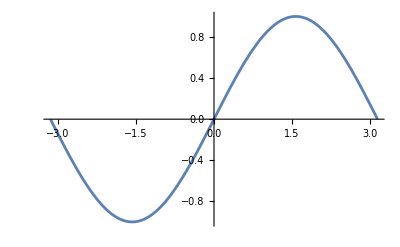

```mathematica
Plot[gslSin[x],{x,-3.14,3.14}]
```

It’s accurate to machine precision, or pretty close.

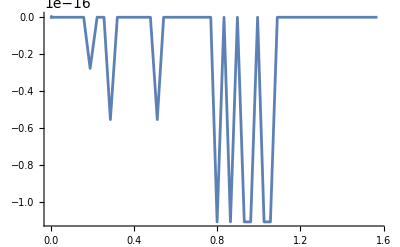

```mathematica
Plot[gslSin[x]-Sin[x],{x,0,Pi/2},WorkingPrecision->24]
```

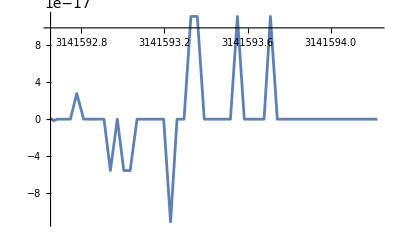

```mathematica
Plot[gslSin[x]-Sin[x],{x,N[π*10^6],N[π*10^6+π/2]},WorkingPrecision->24]
```

```mathematica
RepeatedTiming[gslSin[RandomReal[]],10]
```

{4.58614×10^-6,0.0991604}

## Calling Assembly Language

### sin1.s

This is the most basic approximation, using just the first two terms of the Taylor series, just as a proof that we can write a dynamic library in ARM assembly and call it from C and from Mathematica.

```mathematica
// sin1.s
// Approximate Sin(x) by the Taylor series to degree 3.

.global _sin_1
.p2align 2			// Make sure everything is aligned properly

.text

_sin_1:
        fmul    d1, d0, d0              // d1 = d0^2
        fmul    d1, d1, d0              // d1 = d0^3
        fmov    d2, #6
        fdiv    d1, d1, d2              // d1 = d0^3/6
        fsub    d0, d0, d1              // d0 = d0 - d0^3/6
        ret
```

```mathematica
sin1=ForeignFunctionLoad["./sin/libmysin","sin_1",{"CDouble"}->"CDouble"]
```

ForeignFunction[…]

```mathematica
sin1[0]
```

0.

```mathematica
sin1[N[Pi/2]]
```

0.924832

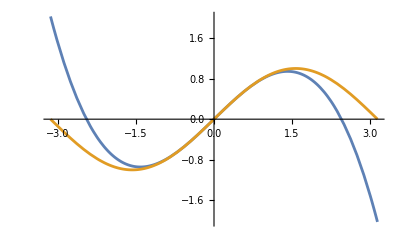

```mathematica
Plot[{sin1[x],Sin[x]},{x,-Pi,Pi}]
```

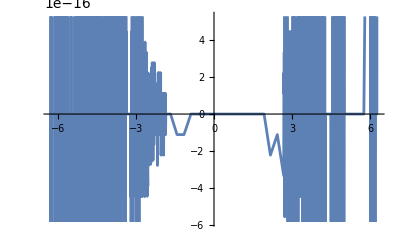

```mathematica
Plot[sin1[x]-(x-x^3/6),{x,-2π,2π},WorkingPrecision->24]
```

```mathematica
Clear[sin2]
sin2=ForeignFunctionLoad["./sin/libmysin","sin_2",{"CDouble"}->"CDouble"]
```

ForeignFunction[…]

```mathematica
sin2[0.0]
```

3.1516×10^-17

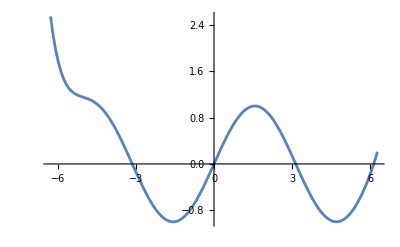

```mathematica
Plot[sin2[x],{x,-2Pi,2Pi}]
```

```mathematica
sin3=ForeignFunctionLoad["./sin/libmysin","sin_3",{"CDouble"}->"CDouble"]
```

ForeignFunction[…]

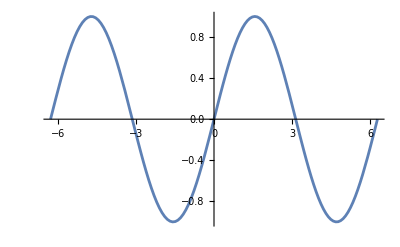

```mathematica
Plot[sin3[x],{x,-2Pi,2Pi}]
```

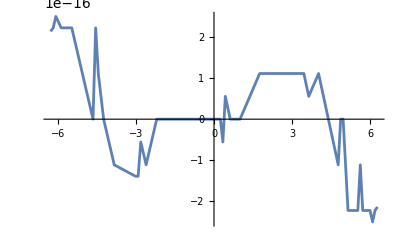

```mathematica
Plot[Sin[x]-sin3[x],{x,-2Pi,2Pi}]
```

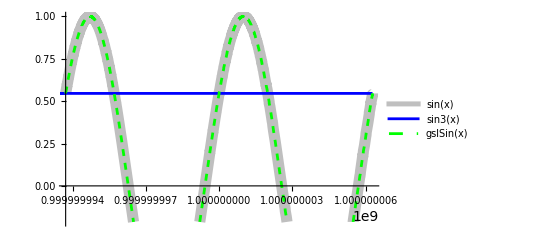

```mathematica
Plot[{Sin[x],sin3[x],gslSin[x]},{x,10^9-2Pi,10^9+2Pi},
PlotLegends->"Expressions",
MaxRecursion->15,
Method->{Refinement->{ControlValue->2°}},
PlotStyle->{{Thickness[0.02],Opacity[0.5],Gray},{Blue},{Dashed,Green}}]
```

```mathematica
|
```

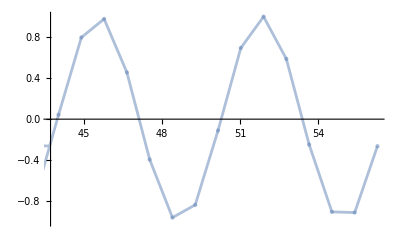

```mathematica
Plot[sin3[x],{x,50-2Pi,50+2Pi},Mesh->All,PlotStyle->{Opacity[0.5]}]
```

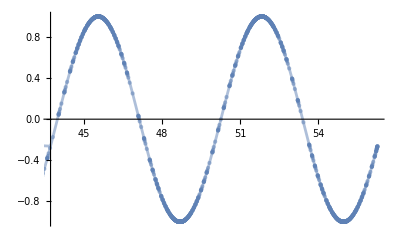

```mathematica
Plot[sin3[x],{x,50-2Pi,50+2Pi},Mesh->All,PlotStyle->{Opacity[0.5]},MaxRecursion->15,
Method->{Refinement->{ControlValue->2°}}]
```

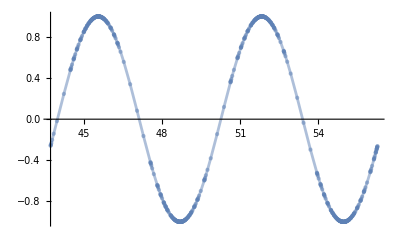

```mathematica
Plot[gslSin[x],{x,50-2Pi,50+2Pi},Mesh->All,PlotStyle->{Opacity[0.5]}]
```

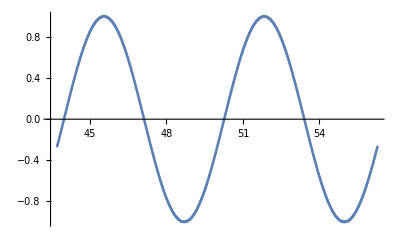

```mathematica
ListPlot[Table[{x,sin3[x]},{x,50-2Pi,50+2Pi,0.01}]]
```

```mathematica
reduce=ForeignFunctionLoad["./sin/libmysin","reduce",{"CDouble"}->"CDouble"]
```

ForeignFunction[…]

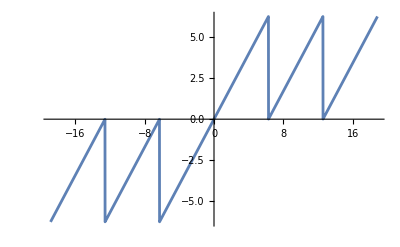

```mathematica
Plot[reduce[x],{x,-6Pi,6Pi}]
```

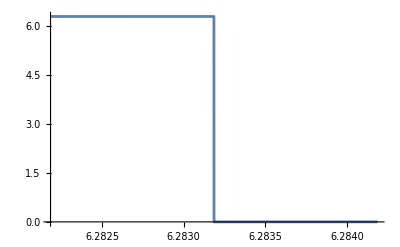

```mathematica
Plot[reduce[x],{x,2Pi-0.001,2Pi+0.001}]
```

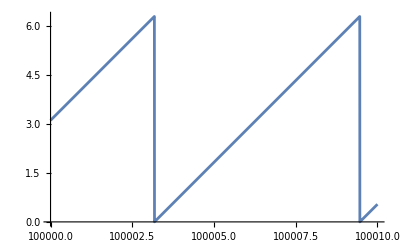

```mathematica
Plot[reduce[x],{x,100000,100010}]
```

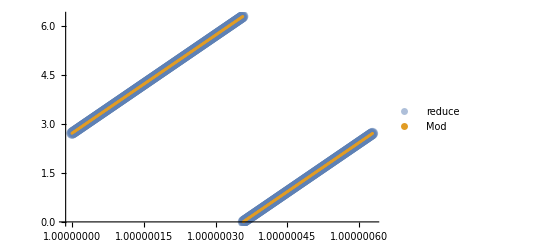

```mathematica
ListPlot[
{Table[{x,reduce[x]},{x,10000000,10000000+2Pi,0.01}],
Table[{x,N[Mod[x,2Pi],24]},{x,10000000,10000000+2Pi,0.01}]},
PlotLegends->{"reduce","Mod"},
PlotStyle->{{PointSize[0.02],Opacity[0.5]},{PointSize[0.005]}}
]
```

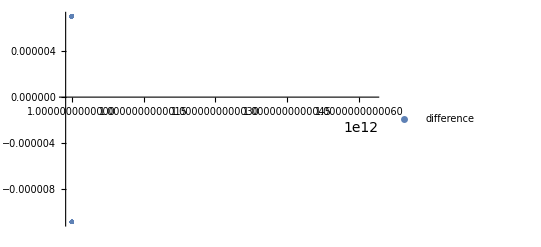

```mathematica
ListPlot[
Table[{x,reduce[x]-N[Mod[x,2Pi],18]},{x,10^12,10^12+2Pi,0.01}],
PlotLegends->{"difference"}]
```

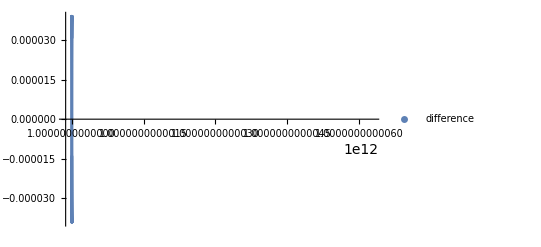

```mathematica
ListPlot[
Table[{x,sin3[x]-gslSin[x]},{x,10^12,10^12+2Pi,0.01}],
PlotLegends->{"difference"}]
```

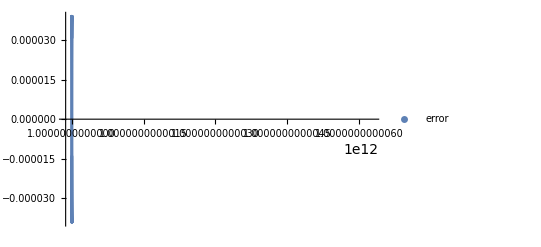

```mathematica
ListPlot[
Table[{x,sin3[x]-N[Sin[x]]},{x,10^12,10^12+2Pi,0.01}],
PlotLegends->{"error"}]
```

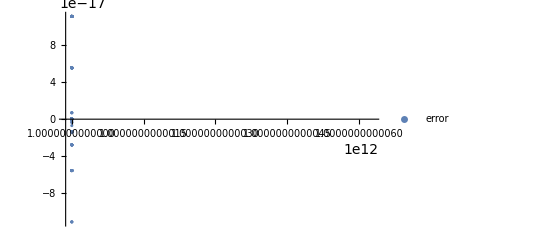

```mathematica
ListPlot[
Table[{x,gslSin[x]-N[Sin[x]]},{x,10^12,10^12+2Pi,0.01}],
PlotLegends->{"error"}]
```

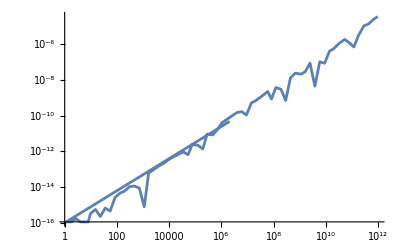

```mathematica
LogLogPlot[(Sin[#]-sin3[#]&)[x],{x,0, 10^12},PlotRange->All]
```

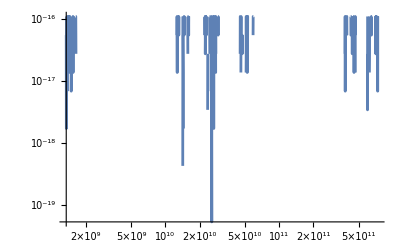

```mathematica
LogLogPlot[(Sin[#]-gslSin[#]&)[x],{x,0, 10^12},PlotRange->All]
```

### GSL Angle Reduction

```mathematica
int
gsl_sf_sin_e(double x, gsl_sf_result * result)
{
  /* CHECK_POINTER(result) */

  {
    const double P1 = 7.85398125648498535156e-1;
    const double P2 = 3.77489470793079817668e-8;
    const double P3 = 2.69515142907905952645e-15;

    const double sgn_x = GSL_SIGN(x);
    const double abs_x = fabs(x);

    if(abs_x < GSL_ROOT4_DBL_EPSILON) {
      const double x2 = x*x;
      result->val = x * (1.0 - x2/6.0);
      result->err = fabs(x*x2*x2 / 100.0);
      return GSL_SUCCESS;
    }
    else {
      double sgn_result = sgn_x;
      double y = floor(abs_x/(0.25*M_PI));
      int octant = y - ldexp(floor(ldexp(y,-3)),3);
      int stat_cs;
      double z;

      if(GSL_IS_ODD(octant)) {
        octant += 1;
        octant &= 07;
        y += 1.0;
      }

      if(octant > 3) {
        octant -= 4;
        sgn_result = -sgn_result;
      }
      
      z = ((abs_x - y * P1) - y * P2) - y * P3;

      if(octant == 0) {
        gsl_sf_result sin_cs_result;
        const double t = 8.0*fabs(z)/M_PI - 1.0;
        stat_cs = cheb_eval_e(&sin_cs, t, &sin_cs_result);
        result->val = z * (1.0 + z*z * sin_cs_result.val);
      }
      else { /* octant == 2 */
        gsl_sf_result cos_cs_result;
        const double t = 8.0*fabs(z)/M_PI - 1.0;
        stat_cs = cheb_eval_e(&cos_cs, t, &cos_cs_result);
        result->val = 1.0 - 0.5*z*z * (1.0 - z*z * cos_cs_result.val);
      }

      result->val *= sgn_result;

      if(abs_x > 1.0/GSL_DBL_EPSILON) {
        result->err = fabs(result->val);
      }
      else if(abs_x > 100.0/GSL_SQRT_DBL_EPSILON) {
        result->err = 2.0 * abs_x * GSL_DBL_EPSILON * fabs(result->val);
      }
      else if(abs_x > 0.1/GSL_SQRT_DBL_EPSILON) {
        result->err = 2.0 * GSL_SQRT_DBL_EPSILON * fabs(result->val);
      }
      else {
        result->err = 2.0 * GSL_DBL_EPSILON * fabs(result->val);
      }

      return stat_cs;
    }
  }
}
```

```mathematica
Clear[gslY,gslZ,gslT,ldexp,octant]
```

```mathematica
gslY[x_]:= Floor[Abs[x]/(0.25*Pi)]
```

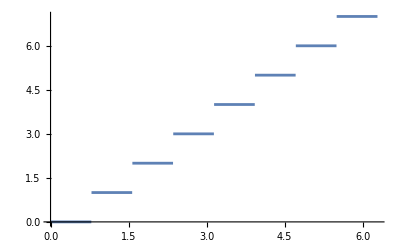

```mathematica
Plot[gslY[x],{x,0,2Pi}]
```

```mathematica
ldexp[x_,c_]:=x*2^c;
```

```mathematica
octant[x_]:=With[{y=gslY[x]},
y - ldexp[Floor[ldexp[y,-3]],3] 
]
```

```mathematica
Plot[octant[x],{x,0,2Pi}]
```

-Graphics-

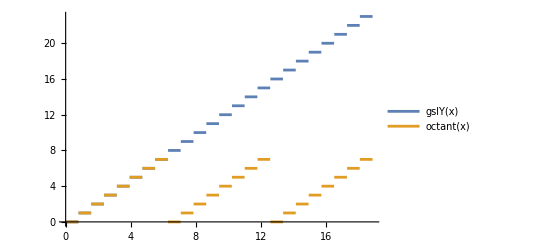

```mathematica
Plot[{gslY[x],octant[x]},{x,0,6Pi},PlotLegends->"Expressions"]
```

```mathematica
gslZ[x_]:=With[{
P1= 7.85398125648498535156*10^-1,
P2= 3.77489470793079817668*10^-8,
P3= 2.69515142907905952645*10^-15,
y = gslY[x]},
(*((Abs[x] - y * P1) - y * P2) - y * P3]*)
result=Abs[x];
result-=y*P1;
result-=y*P2;
result-=y*P3;
result]
```

```mathematica
gslZ[3.14]
```

0.783806

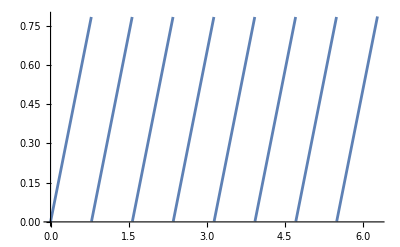

```mathematica
Plot[gslZ[x],{x,0,2Pi}]
```

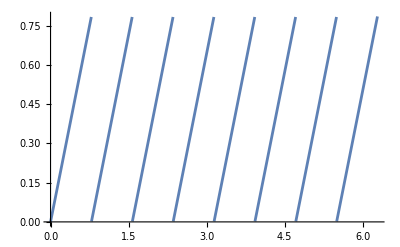

```mathematica
Plot[Mod[x,Pi/4],{x,0,2Pi}]
```

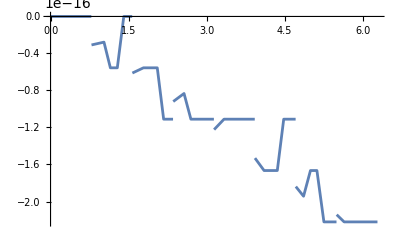

```mathematica
Plot[gslZ[x]-Mod[x,Pi/4],{x,0,2Pi}]
```

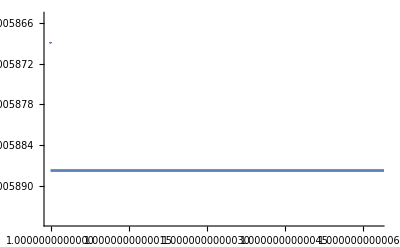

```mathematica
Plot[gslZ[x]-Mod[x,Pi/4],{x,10^12,10^12+2Pi}]
```

This z is the reduced angle from the GSL sin routine, and it should be comparable to

```mathematica
gslT[x_]:=8.0*Abs[gslZ[x]]/Pi - 1.0
```

```mathematica
gslT[3.14]
```

0.995944

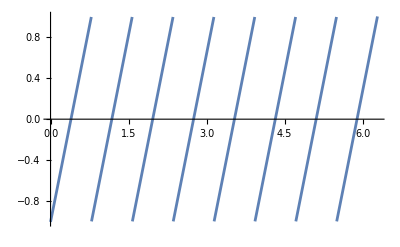

```mathematica
Plot[gslT[x],{x,0,2Pi}]
```

```mathematica
gslReduce[x_]:=N[(gslT[x]+1)*π/8,50]
```

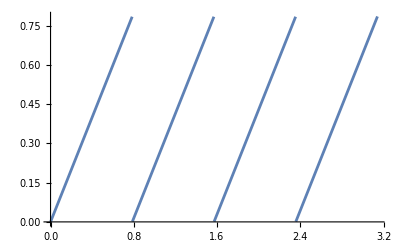

```mathematica
Plot[gslReduce[x],{x,0,π}]
```

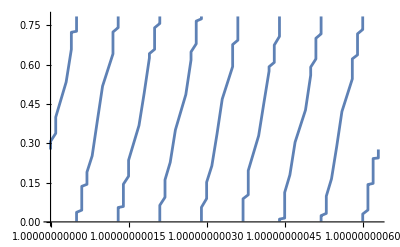

```mathematica
Plot[gslReduce[x],{x,10^10,2π+10^10}]
```

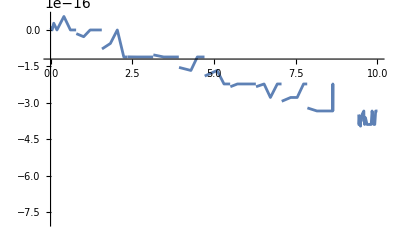

```mathematica
Plot[gslReduce[x]-Mod[x,π/4],{x,0,10}]
```

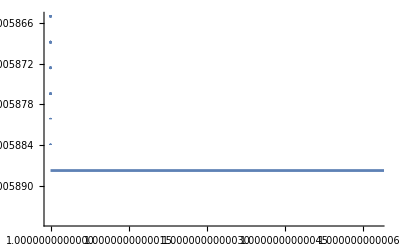

```mathematica
Plot[gslReduce[x]-N[Mod[x,π/4],24],{x,10^12,2π+10^12}]
```

Why is the error in this so large?

```mathematica
gslReduceExt=ForeignFunctionLoad["./sin/libangle_reduction","gslReduce",{"CDouble"}->"CDouble"]
```

ForeignFunction[…]

```mathematica
NumberForm[gslReduceExt[1.0],17]
```

-0.4535209105296746

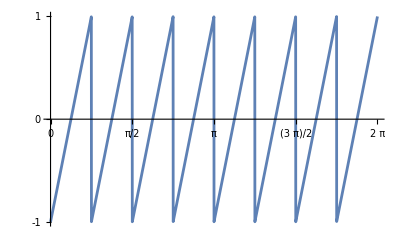

```mathematica
Plot[gslReduceExt[x],{x,0,2Pi},Ticks->{Table[n*Pi/4,{n,0,8}],{-1,0,1}}]
```

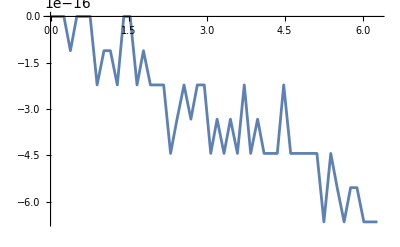

```mathematica
Plot[gslReduceExt[x]-N[Mod[x,π/4]/(π/8)-1,24],{x,0,2π}]
```

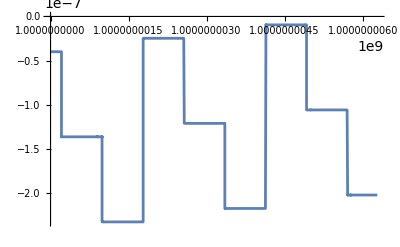

```mathematica
Plot[gslReduceExt[x]-N[Mod[x,π/4]/(π/8)-1,24],{x,10^9,2π+10^9}]
```

```mathematica
xpoints=Table[x,{x,10^9,2π+10^9,0.01}];
errors=(gslReduceExt[#]-N[Mod[#,π/4]/(π/8)-1,24]&)/@xpoints;
```

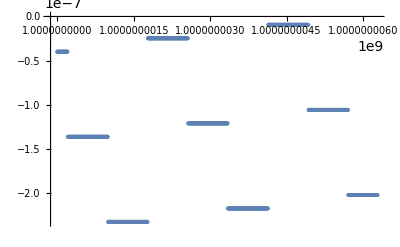

```mathematica
ListPlot[Transpose[{xpoints,errors}]]
```

```mathematica
$MaxExtraPrecision=200;
x=1000000000001;
a=gslReduceExt[x];
b=Mod[x,π/4]/(π/8)-1;
{NumberForm[a,17],NumberForm[N[b,18],17]}//TableForm
d=NumberForm[a-N[b,24],17]
```

-0.1281486083894606
-0.12814860838946067

2.775557561562891×10^-17

```mathematica
{#,Precision[Symbol[#]],Accuracy[Symbol[#]]}&/@{"a","b","d"}//TableForm
```

a | MachinePrecision | 16.8469
b | ∞ | ∞
d | MachinePrecision | 32.5112

```mathematica
a=-0.1281486083894606
b=-0.12814860838946067
d=a-b
```

-0.128149

-0.128149

8.32667×10^-17

```mathematica
{#,Precision[Symbol[#]],Accuracy[Symbol[#]]}&/@{"a","b","d"}//TableForm
```

a | MachinePrecision | 16.8469
b | MachinePrecision | 16.8469
d | MachinePrecision | 32.0341